```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\mouze\Desktop\CM_labs\lab4

```mathematica
polyU = Import["test8_u.txt","Table"][[1]]
polyC = Import["test8_c.txt","Table"][[1]]
LagrangePolynomU = ∑_(k=1)^(Length@polyU) polyU[[k]]*x^(Length@polyU-k)
LagrangePolynomC = ∑_(k=1)^(Length@polyU) polyC[[k]]*x^(Length@polyC-k)
```

{-1.23865,0.503065,5.53577,1.84023,-6.74896,5.14561,6.95892,-7.55814,-2.1335}

{-1.40002,-0.0877519,5.82078,2.82908,-6.89228,4.70434,6.97701,-7.51241,-2.1335}

-2.1335-7.55814 x+6.95892 x^2+5.14561 x^3-6.74896 x^4+1.84023 x^5+5.53577 x^6+0.503065 x^7-1.23865 x^8

-2.1335-7.51241 x+6.97701 x^2+4.70434 x^3-6.89228 x^4+2.82908 x^5+5.82078 x^6-0.0877519 x^7-1.40002 x^8

```mathematica
f =(4x^3+2x^2-4x+2)^(√2)+ ArcSin[1/(5+x -x^2)]-5
```

-5+(2-4 x+2 x^2+4 x^3)^(√2)+ArcSin[1/(5+x-x^2)]

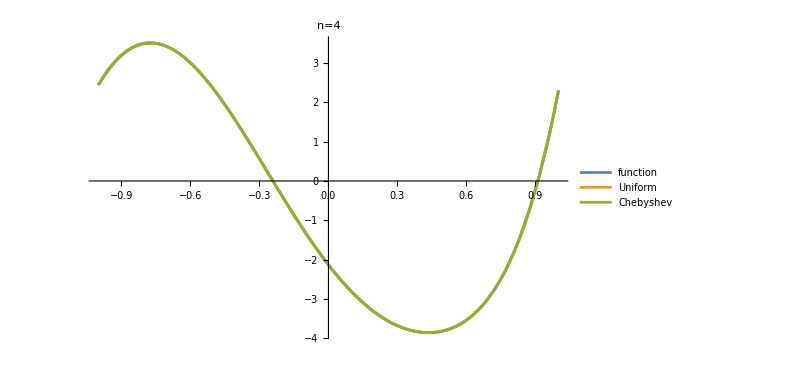

```mathematica
g = Plot[{f, LagrangePolynomU,LagrangePolynomC},{x,-1,1},ImageSize->600,PlotLegends->{"function", "Uniform", "Chebyshev"}, PlotLabel->"n=4"]
```

```mathematica
Export["test8.png",g]
```

test8.png

```mathematica
f=((x-1)(x-2)(x-3))/((0-1)(0-2)(0-3)) + ((x)(x-2)(x-3))/((1-2)(1-3))E +((x)(x-1)(x-3))/((2)(2-1)(2-3))E^2 + ((x)(x-1)(x-2))/((3)(3-1)(3-2))E^3 // N //Expand
```

1.+1.93311 x-1.06036 x^2+0.845536 x^3

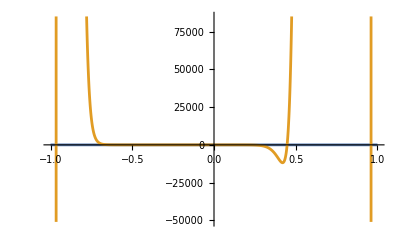

```mathematica
Plot[{E^x, LagrangePolynom},{x,-1,1}]
```

```mathematica
((x-1)(x-2)(x-3))/((0-1)(0-2)(0-3)) +  ((x)(x-2)(x-3))/((1-2)(1-3))E + ((x)(x-1)(x-3))/((2)(2-1)(2-3))E^2 +((x)(x-1)(x-2))/((3)(3-1)(3-2))E^3// Expand // N
```

1.+1.93311 x-1.06036 x^2+0.845536 x^3

```mathematica
(x-1)(x-2)//Expand
```

2-3 x+x^2

```mathematica
0*x^36+0*x^35+0*x^34+0*x^33+0*x^32+0*x^31+0*x^30+0*x^29+0*x^28+0*x^27+0*x^26+0*x^25+0*x^24+0*x^23+0*x^22+0*x^21+0*x^20+0*x^19+-5.95069 * 10^-11*x^18+5.64835* 10^-9*x^17+-2.46864* 10^-7*x^16+6.58669* 10^-6*x^15+-0.00011993*x^14+0.00157794*x^13+-0.0154962*x^12+0.115689*x^11+-0.66253*x^10+2.91581*x^9+-9.81654*x^8+24.9982*x^7+-47.2285*x^6+64.1918*x^5+-59.7036*x^4+34.6696*x^3+-9.96789*x^2+-0.0935224*x+1.27522  /. x->6.79
```

-342.13

```mathematica
0.7*(-6*0.3+4) + (1-0.7)(-3*0.3 + 2)
```

1.87

```mathematica
0.7*0.3 + 0.7 + 0.3 +1
```

2.21

```mathematica
9.02501 - Exp[2.2]
```

-3.49943×10^-6

```mathematica
0.2^11 Exp[2]
```

1.51328×10^-7

```mathematica
(n+1)(2^{n-1}*(n-1)*(n-1)+1) // Expand
```

{1+2^(-1+n)+n+2^(-1+n) n-2^n n+2^(-1+n) n^2-2^n n^2+2^(-1+n) n^3}